```mathematica
a={x,y,z};
pos={x,y,z};
```

```mathematica
p0=.
EDipole2[x_,y_,z_,p0_]=(3p0/(x^2+y^2+z^2)^5)*{x*y,y^2-(x^2+y^2+z^2),z*y};
EPoint[x_,y_,z_]=1/(x^2+y^2+z^2)^2.5*{x,y,z};

EDipole[x_,y_,z_,p0_]=EPoint[x,y,z];

EHat[x_,y_,z_,p0_]=EDipole[x,y,z,p0]/(EDipole[x,y,z,p0][[1]]^2+EDipole[x,y,z,p0][[2]]^2+EDipole[x,y,z,p0][[3]]^2)^.5
Curv[x_,y_,z_,p0_]=Table[Sum[EHat[x,y,z,p0][[i]]*D[EHat[x,y,z,p0][[j]],a[[i]]],{i,1,3}],{j,1,3}];
```

{x/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5),y/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5),z/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)}

```mathematica
(EDipole[x,y,z,p0][[1]]^2+EDipole[x,y,z,p0][[2]]^2+EDipole[x,y,z,p0][[3]]^2)^.5
```

(x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5

```mathematica
Curv[x,y,z,p0] // MatrixForm
```

((y (-(0.5 x (-(10. x^2 y)/((x^2+y^2+z^2)^6.)-(10. y^3)/((x^2+y^2+z^2)^6.)-(10. y z^2)/((x^2+y^2+z^2)^6.)+(2 y)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. x y)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+(z (-(0.5 x (-(10. x^2 z)/((x^2+y^2+z^2)^6.)-(10. y^2 z)/((x^2+y^2+z^2)^6.)-(10. z^3)/((x^2+y^2+z^2)^6.)+(2 z)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. x z)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+(x (-(0.5 x (-(10. x^3)/((x^2+y^2+z^2)^6.)-(10. x y^2)/((x^2+y^2+z^2)^6.)-(10. x z^2)/((x^2+y^2+z^2)^6.)+(2 x)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. x^2)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+1/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)
(x (-(0.5 y (-(10. x^3)/((x^2+y^2+z^2)^6.)-(10. x y^2)/((x^2+y^2+z^2)^6.)-(10. x z^2)/((x^2+y^2+z^2)^6.)+(2 x)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. x y)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+(z (-(0.5 y (-(10. x^2 z)/((x^2+y^2+z^2)^6.)-(10. y^2 z)/((x^2+y^2+z^2)^6.)-(10. z^3)/((x^2+y^2+z^2)^6.)+(2 z)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. y z)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+(y (-(0.5 y (-(10. x^2 y)/((x^2+y^2+z^2)^6.)-(10. y^3)/((x^2+y^2+z^2)^6.)-(10. y z^2)/((x^2+y^2+z^2)^6.)+(2 y)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. y^2)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+1/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)
(x (-(0.5 z (-(10. x^3)/((x^2+y^2+z^2)^6.)-(10. x y^2)/((x^2+y^2+z^2)^6.)-(10. x z^2)/((x^2+y^2+z^2)^6.)+(2 x)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. x z)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+(y (-(0.5 z (-(10. x^2 y)/((x^2+y^2+z^2)^6.)-(10. y^3)/((x^2+y^2+z^2)^6.)-(10. y z^2)/((x^2+y^2+z^2)^6.)+(2 y)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. y z)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+(z (-(0.5 z (-(10. x^2 z)/((x^2+y^2+z^2)^6.)-(10. y^2 z)/((x^2+y^2+z^2)^6.)-(10. z^3)/((x^2+y^2+z^2)^6.)+(2 z)/((x^2+y^2+z^2)^5.)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^1.5)-(5. z^2)/((x^2+y^2+z^2)^3.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)+1/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)))/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5))

# Plot

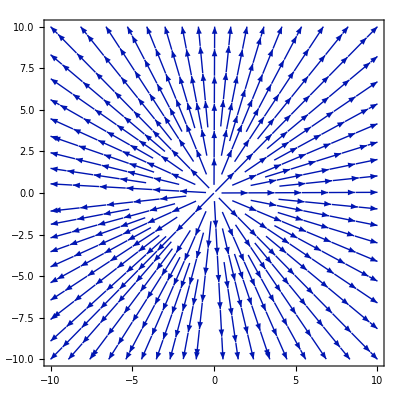

```mathematica
StreamPlot[{EDipole[x,y,0,5][[1]],EDipole[x,y,0,5][[2]]},{x,-10,10},{y,-10,10}]
```

```mathematica
dataE=.
dataC=.
uMin=-6.0;
uMax = 6.0;
vMin = -6.0;
vMax=6.0;
NumPoints=100000;
pts=RandomReal[{uMin,uMax},{NumPoints, 2}];
pts3D=Map[Append[#,0]&,pts];
p0=3;
dataE=Transpose[EDipole[pts3D[[All,1]],pts3D[[All,2]],pts3D[[All,3]],p0]];
dataE=(dataE[[All,1]]^2+dataE[[All,2]]^2+dataE[[All,3]]^2)^.5;
dataC=Transpose[Curv[pts3D[[All,1]],pts3D[[All,2]],pts3D[[All,3]],p0]];
ListPlot[Transpose[{Log[dataE],Log[dataC]}]]
```

$Aborted

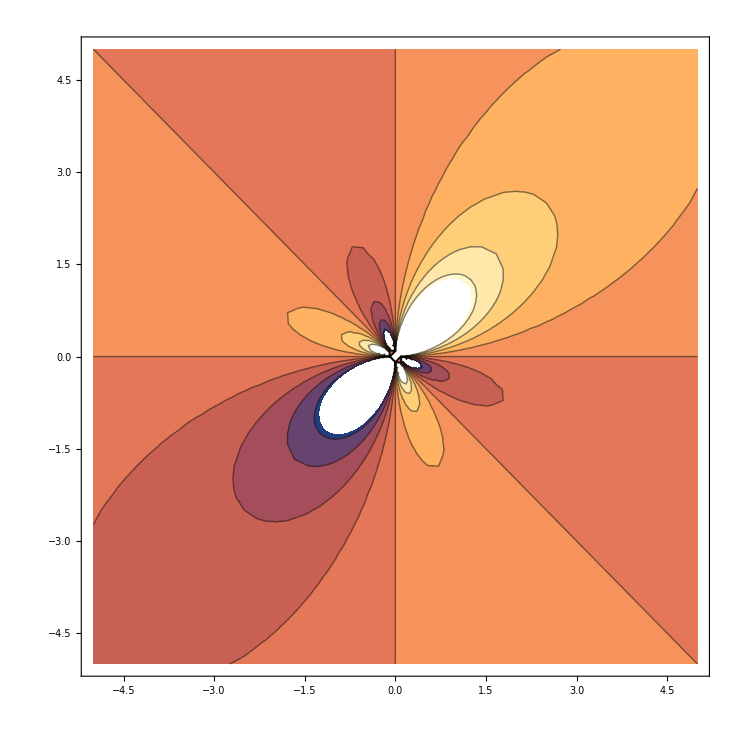

```mathematica
ContourPlot[Curv[u,v,0,p0],{u,-5,5},{v,-5,5}]
```

```mathematica
Curv[0,0,0,p0]
```

Power::infy: Infinite expression 1/0^2.5 encountered.

Power::infy: Infinite expression 1/0^5. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^5. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
Curv[x,y,0,p0]
```

(x (-(0.5 x (0.-(10. x^3)/((x^2+y^2)^6.)-(10. x y^2)/((x^2+y^2)^6.)+(2 x)/((x^2+y^2)^5.)))/((x^2+y^2)^2.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^1.5)-(5. x^2)/((x^2+y^2)^3.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^0.5)+1/((x^2+y^2)^2.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^0.5)))/((x^2+y^2)^2.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^0.5)+(y (-(0.5 y (0.-(10. x^2 y)/((x^2+y^2)^6.)-(10. y^3)/((x^2+y^2)^6.)+(2 y)/((x^2+y^2)^5.)))/((x^2+y^2)^2.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^1.5)-(5. y^2)/((x^2+y^2)^3.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^0.5)+1/((x^2+y^2)^2.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^0.5)))/((x^2+y^2)^2.5 (x^2/((x^2+y^2)^5.)+y^2/((x^2+y^2)^5.))^0.5)

```mathematica
Test1[x_,y_,z_]={x/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5),y/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5),z/((x^2+y^2+z^2)^2.5 (x^2/((x^2+y^2+z^2)^5.)+y^2/((x^2+y^2+z^2)^5.)+z^2/((x^2+y^2+z^2)^5.))^0.5)};
```

```mathematica
Test2[x_,y_,z_]={x/((x^2+y^2+z^2)^1.5),y/((x^2+y^2+z^2)^1.5),z/((x^2+y^2+z^2)^1.5)};
```

```mathematica
Solve[Test1[x,y,z]==Test2[x,y,z]]
```

{{z→-0.5 √(-2. (2. x^2+2. y^2)-2. √((2. x^2+2. y^2)^2-4. (-1.+1. x^4+2. x^2 y^2+1. y^4)))},{z→0.5 √(-2. (2. x^2+2. y^2)-2. √((2. x^2+2. y^2)^2-4. (-1.+1. x^4+2. x^2 y^2+1. y^4)))},{z→-0.5 √(-2. (2. x^2+2. y^2)+2. √((2. x^2+2. y^2)^2-4. (-1.+1. x^4+2. x^2 y^2+1. y^4)))},{z→0.5 √(-2. (2. x^2+2. y^2)+2. √((2. x^2+2. y^2)^2-4. (-1.+1. x^4+2. x^2 y^2+1. y^4)))},{y→-0.5 √(-4. x^2+2. √(4. x^4-4. (-1.+1. x^4))),z→0.},{y→0.5 √(-4. x^2+2. √(4. x^4-4. (-1.+1. x^4))),z→0.},{y→0.,z→-0.5 √(-4. x^2+2. √(4. x^4-4. (-1.+1. x^4)))},{y→0.,z→0.5 √(-4. x^2+2. √(4. x^4-4. (-1.+1. x^4)))},{x→0.,z→-0.5 √(-4. y^2+2. √(4. y^4-4. (-1.+1. y^4)))},{x→0.,z→0.5 √(-4. y^2+2. √(4. y^4-4. (-1.+1. y^4)))},{x→-1.,y→0.,z→0.},{x→1.,y→0.,z→0.},{x→0.,y→-1.,z→0.},{x→0.,y→1.,z→0.},{x→0.,y→0.,z→-1.},{x→0.,y→0.,z→1.}}